```mathematica
CloseStreams[];
t=With[
{lastPrimeIndex=43, tupleLength=2},
Flatten[
Monitor[
Table[
Table[Append[mingle, 
If[magicGraham[mingle]>0,CachedRatioFor[mingle],0]],{mingle, Permutations[tuple]}]
,
{tuple,Subsets[Prime[Range[2,lastPrimeIndex]],{tupleLength}]}
],
tuple
]
,1
]
];
"done"
```

done

```mathematica
CloseStreams[]
```

```mathematica
CachedRatioFor[{3,5}]
```

0.336009

```mathematica
CachedRatioFor[{3,7}]
```

0.376329

```mathematica
N[Log[3]]
```

1.09861

```mathematica
N[Log[7]]
```

1.94591

```mathematica
N[Log[5]]
```

1.60944

```mathematica
1/N[Log[5*7]]
```

0.281266

```mathematica
CachedRatioFor[{5,7}]
```

0.447902

```mathematica
CachedRatioFor[{3,5,7}]
```

0.028661

```mathematica
keep=Table[
Module[{couples, triple},
couples=Sum[CachedRatioFor[couple], {couple,Subsets[tuple,{2}] }];
triple= CachedRatioFor[tuple];
{couples, triple}
]
,{tuple, Map[#[[1]]&,Select[ReadList[RatioCacheFileName],Length[#[[1]]]==3&]]}
];
"done"
```

$Aborted

done

```mathematica
CloseStreams[];
Table[
CachedRatioFor[tuple]
,{tuple, Subsets[Prime[Range[2,102,10]],{3}]}
]
```

$Aborted

```mathematica
Table[Subsets[t,{2}],{t,Permutations[{3,5,7}]}]
```

{{{3,5},{3,7},{5,7}},{{3,7},{3,5},{7,5}},{{5,3},{5,7},{3,7}},{{5,7},{5,3},{7,3}},{{7,3},{7,5},{3,5}},{{7,5},{7,3},{5,3}}}

```mathematica
Table[
tuple
,{tuple, Subsets[Prime[Range[2,102,10]],{3}]}
]
```

{{3,37,79},{3,37,131},{3,37,181},{3,37,239},{3,37,293},{3,37,359},{3,37,421},{3,37,479},{3,37,557},{3,79,131},{3,79,181},{3,79,239},{3,79,293},{3,79,359},{3,79,421},{3,79,479},{3,79,557},{3,131,181},{3,131,239},{3,131,293},{3,131,359},{3,131,421},{3,131,479},{3,131,557},{3,181,239},{3,181,293},{3,181,359},{3,181,421},{3,181,479},{3,181,557},{3,239,293},{3,239,359},{3,239,421},{3,239,479},{3,239,557},{3,293,359},{3,293,421},{3,293,479},{3,293,557},{3,359,421},{3,359,479},{3,359,557},{3,421,479},{3,421,557},{3,479,557},{37,79,131},{37,79,181},{37,79,239},{37,79,293},{37,79,359},{37,79,421},{37,79,479},{37,79,557},{37,131,181},{37,131,239},{37,131,293},{37,131,359},{37,131,421},{37,131,479},{37,131,557},{37,181,239},{37,181,293},{37,181,359},{37,181,421},{37,181,479},{37,181,557},{37,239,293},{37,239,359},{37,239,421},{37,239,479},{37,239,557},{37,293,359},{37,293,421},{37,293,479},{37,293,557},{37,359,421},{37,359,479},{37,359,557},{37,421,479},{37,421,557},{37,479,557},{79,131,181},{79,131,239},{79,131,293},{79,131,359},{79,131,421},{79,131,479},{79,131,557},{79,181,239},{79,181,293},{79,181,359},{79,181,421},{79,181,479},{79,181,557},{79,239,293},{79,239,359},{79,239,421},{79,239,479},{79,239,557},{79,293,359},{79,293,421},{79,293,479},{79,293,557},{79,359,421},{79,359,479},{79,359,557},{79,421,479},{79,421,557},{79,479,557},{131,181,239},{131,181,293},{131,181,359},{131,181,421},{131,181,479},{131,181,557},{131,239,293},{131,239,359},{131,239,421},{131,239,479},{131,239,557},{131,293,359},{131,293,421},{131,293,479},{131,293,557},{131,359,421},{131,359,479},{131,359,557},{131,421,479},{131,421,557},{131,479,557},{181,239,293},{181,239,359},{181,239,421},{181,239,479},{181,239,557},{181,293,359},{181,293,421},{181,293,479},{181,293,557},{181,359,421},{181,359,479},{181,359,557},{181,421,479},{181,421,557},{181,479,557},{239,293,359},{239,293,421},{239,293,479},{239,293,557},{239,359,421},{239,359,479},{239,359,557},{239,421,479},{239,421,557},{239,479,557},{293,359,421},{293,359,479},{293,359,557},{293,421,479},{293,421,557},{293,479,557},{359,421,479},{359,421,557},{359,479,557},{421,479,557}}

```mathematica
keep
```

{{1.16024,0.028661},{1.26634,0.06945},{1.3019,0.082381},{1.35536,0.101588},{1.37518,0.108625},{1.40301,0.124294},{1.44167,0.137113},{1.45666,0.142755},{1.48523,0.15442},{1.35453,0.102724},{1.39161,0.11752},{1.4477,0.139812},{1.47328,0.146087},{1.50322,0.162433},{1.53953,0.177867},{1.55101,0.181708},{1.57586,0.192731},{1.48703,0.161688},{1.55393,0.185622},{1.57836,0.194601},{1.6148,0.208413},{1.65409,0.225185},{1.66632,0.230453},{1.69534,0.243417},{1.58301,0.200564},{1.60901,0.208916},{1.64778,0.225039},{1.68897,0.241124},{1.70153,0.246286},{1.73072,0.259382},{1.65158,0.232917},{1.69445,0.247847},{1.73907,0.266176},{1.75246,0.271676},{1.78342,0.285931},{1.71087,0.256805},{1.75695,0.275201},{1.77066,0.281938},{1.80212,0.294552},{1.78226,0.292067},{1.79659,0.297884},{1.82939,0.310217},{1.82458,0.314246},{1.85798,0.330341},{1.86745,0.332741},{1.5021,0.166542},{1.54268,0.182617},{1.59933,0.206149},{1.62459,0.214649},{1.65273,0.229377},{1.69385,0.247288},{1.70755,0.252283},{1.73294,0.264089},{1.64253,0.229247},{1.70999,0.255463},{1.7341,0.265296},{1.76874,0.278755},{1.81284,0.297886},{1.82728,0.303556},{1.85684,0.316138},{1.74257,0.270443},{1.76825,0.280828},{1.80522,0.29607},{1.85122,0.316118},{1.866,0.321245},{1.89573,0.335837},{1.81137,0.30406},{1.85245,0.322331},{1.90188,0.344245},{1.91749,0.349656},{1.94899,0.3622},{1.86854,0.333112},{1.91944,0.354096},{1.93536,0.360826},{1.96737,0.376936},{1.94295,0.370249},{1.95949,0.377122},{1.99283,0.391501},{1.9923,0.396038},{2.02624,0.409679},{2.03792,0.414521},{1.73979,0.269988},{1.80987,0.298945},{1.83975,0.310732},{1.87649,0.328516},{1.91824,0.347128},{1.92917,0.352986},{1.95502,0.365827},{1.84398,0.314294},{1.87543,0.327447},{1.9145,0.344397},{1.95815,0.365041},{1.96942,0.370336},{1.99544,0.386411},{1.92118,0.353306},{1.96435,0.37157},{2.01143,0.39375},{2.02353,0.400021},{2.05132,0.414241},{1.98622,0.382669},{2.03477,0.40763},{2.04718,0.419171},{2.07547,0.426215},{2.06037,0.419638},{2.0734,0.426266},{2.10303,0.441967},{2.10386,0.444034},{2.13409,0.459426},{2.14227,0.464696},{1.94396,0.368367},{1.97425,0.380008},{2.01983,0.400204},{2.06646,0.421743},{2.07847,0.426037},{2.10866,0.441353},{2.03081,0.405712},{2.08049,0.429163},{2.13055,0.454137},{2.1434,0.461365},{2.17535,0.477457},{2.1012,0.436197},{2.15273,0.46414},{2.16588,0.471616},{2.19834,0.488915},{2.18484,0.480947},{2.19861,0.487176},{2.23241,0.505243},{2.23205,0.505769},{2.26644,0.524637},{2.27537,0.529306},{2.05849,0.423349},{2.1105,0.444832},{2.16246,0.47125},{2.17564,0.478509},{2.20776,0.49387},{2.13278,0.455935},{2.18621,0.483136},{2.1997,0.490464},{2.23233,0.507516},{2.22065,0.501263},{2.23476,0.506574},{2.26873,0.526444},{2.2701,0.526482},{2.30466,0.545739},{2.31392,0.549349},{2.16911,0.478647},{2.22597,0.506544},{2.24029,0.512796},{2.27469,0.530304},{2.26451,0.525752},{2.27946,0.532335},{2.31519,0.553389},{2.31822,0.550877},{2.35455,0.572468},{2.36464,0.576499},{2.27867,0.534675},{2.29393,0.5425},{2.33017,0.560825},{2.33416,0.562345},{2.371,0.58182},{2.3814,0.586203},{2.35576,0.577315},{2.39393,0.597021},{2.40496,0.604091},{2.4277,0.621347}}

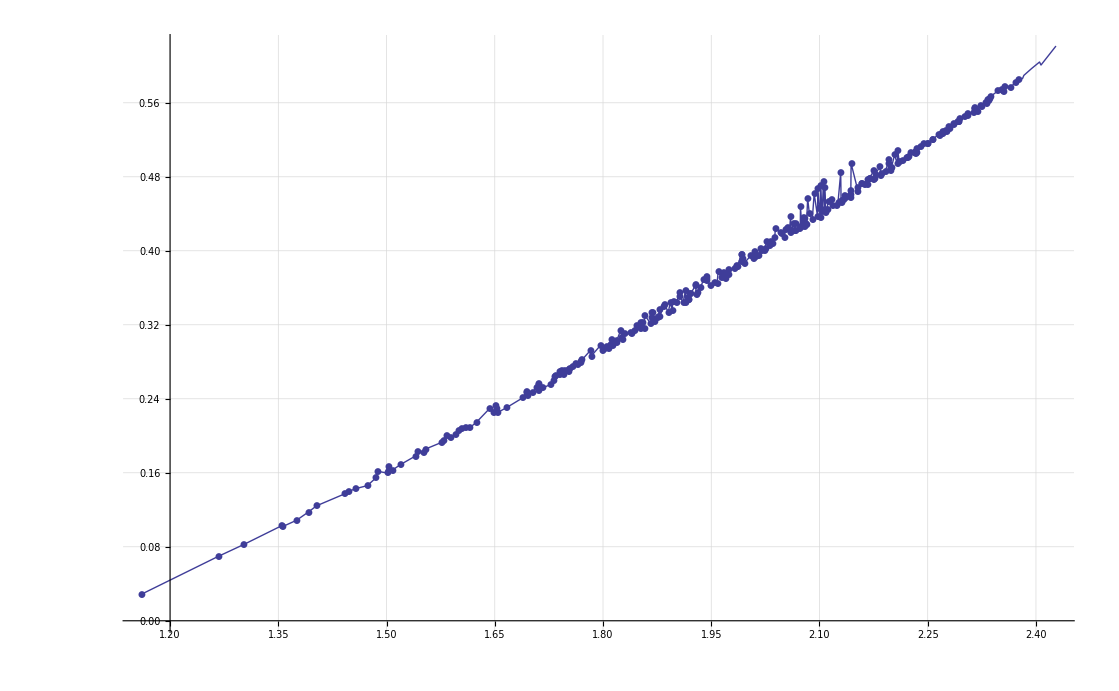

```mathematica
ListLinePlot[Sort[keep], PlotMarkers->Automatic, GridLines->Automatic]
```

```mathematica
CachedRatioFor[{3,5,7,11 }]
```

0

```mathematica
FindFit[keep,a x+b,{a,b},x]
```

{a→0.481698,b→-0.567077}

```mathematica
FindFit[keep,a x+b,{a,b},x]
```

{a→0.474039,b→-0.553068}